Author : Celestine P . Lawrence 
Date : 16/06/22 
Runtime : ~2 mins using Wolfram Mathematica 13.0 on a HP Slim Desktop S01 - pF1000nd  
Results: Compact model of  nanocluster functionality, a physics-based Linear-Min neural network  model, utility of the compact model to emulate a linear-nonlinear  network  for pattern recognition

Data obtained from a nanomaterial cluster of dopant atoms with 7 input electrodes and 1 output electrode.   Check section 6.2 of https://research.utwente.nl/en/publications/evolving-networks-to-have-intelligence-realized-at-nanoscale for a detailed description, specifically Figure 6.4 for the device geometry, and Figure 6.3 (run #1) for the output values (in pA).

```mathematica
outY={0.0953,625.,84.4,270.,6.47,716.,72.2,212.,218.,522.,215.,341.,216.,580.,213.,315.,64.,509.,75.9,206.,60.5,477.,79.1,206.,279.,487.,280.,385.,278.,462.,278.,387.,2.34,649.,182.,203.,11.7,598.,65.1,167.,223.,539.,251.,316.,215.,553.,208.,305.,60.9,461.,78.7,205.,62.1,388.,69.6,206.,278.,475.,276.,390.,273.,437.,270.,392.,-3.87,580.,96.9,223.,6.57,582.,78.,180.,219.,499.,215.,318.,212.,539.,213.,309.,60.4,450.,77.2,207.,63.2,430.,79.4,205.,289.,481.,280.,391.,279.,470.,273.,386.,1.97,618.,196.,193.,9.02,584.,67.3,161.,255.,525.,270.,319.,227.,499.,221.,309.,60.8,422.,77.4,201.,61.3,349.,69.6,207.,277.,477.,275.,390.,269.,438.,270.,395.};
```

A 2-factor weighted sum model generalizes well for the nanocluster, with a high test-correlation.

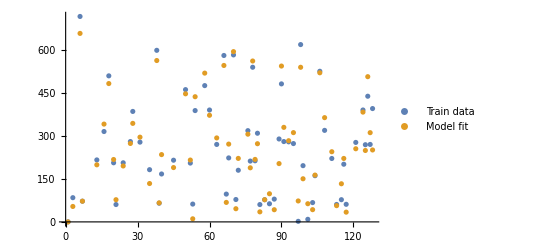

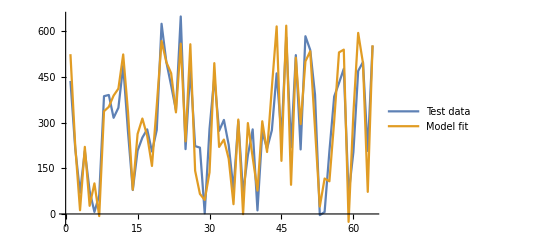

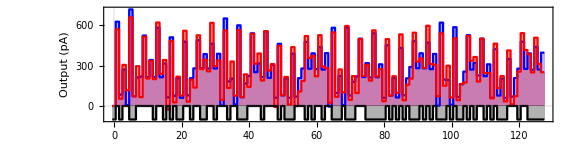

```mathematica
split=RandomSample[Range[128]]; (*random permutation of dataset*)
trainI=split[[;;64]];testI=split[[65;;]]; (*50-50 train-test split*)
inX=1.*Table[ x=IntegerDigits[i,2,7];Flatten@Outer[Times,x,x],{i,0,127}]; (* 2-factor weighted sum, 49 parameters *)
trainX=inX[[trainI]];testX=inX[[testI]];trainY=outY[[trainI]];testY=outY[[testI]];
ListPlot[ {Transpose@{trainI,trainY},Transpose@{trainI,trainX . (PseudoInverse[trainX] . trainY)}},PlotLegends->{"Train data","Model fit"}]
ListLinePlot[ {testY,testX . (LeastSquares[trainX,trainY])},PlotLegends->{"Test data","Model fit"}]
r=Table[0,128];r[[trainI]]=-100;
ListStepPlot[ 
{{Range[128]-1,outY}ᵀ,{Range[128]-1,inX . (PseudoInverse[trainX] . trainY)}ᵀ,{Range[128]-1,r}ᵀ},Center,
PlotLegends->{"Test data","Model"},Filling->Axis,PlotTheme->"Scientific",PlotStyle->{Blue,Red,Black},AspectRatio->1/4,ImageSize->Large, 
FrameLabel->{"Configuration number","Output (pA)"}]
```

We can obtain for comparison, the correlations for a linear fit and 2-factor fit.

```mathematica
eval[split_,inX_]:=(
trainI=split[[;;64]];testI=split[[65;;]];
trainX=inX[[trainI]];
testX=inX[[testI]];
trainY=outY[[trainI]];
testY=outY[[testI]];
weights=PseudoInverse[trainX] . trainY;
{Correlation[trainY,trainX . weights],
Correlation[testY,testX . weights]})
eval12[split_]:={eval[split, inX1=1.*Table[ x=IntegerDigits[i,2,7];x,{i,0,127}] ],eval[split, inX2=1.*Table[ x=IntegerDigits[i,2,7];Flatten@Outer[Times,x,x],{i,0,127}] ]}
```

Results for fitting methods over 100 random train-test splits.

```mathematica
results= Table[ eval12[ RandomSample[Range[128]] ],{100}];
Mean@results
StandardDeviation@results
```

{{0.807421,0.784751},{0.971362,0.919827}}

{{0.0296189,0.0398204},{0.00619473,0.018486}}

Physics-based modelling is more accurate, but slower to fit.

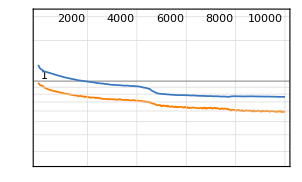
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:40000  rounds:10000  time:31s  examples/s:33611
data | ,,  training examples:104  validation examples:26  processed examples:1040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size26CPU
round | ,,  loss:6.12×10^-1
validation | ,,  loss:7.63×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

Model | Linear multinomial | Quadratic multinomial | Min over 8 linear multinomials
Correlation | 0.802335 | 0.961779 | 0.786878
MSE | 1233.45 | 536.664 | 1498.4

```mathematica
inX=1.*Table[ x=IntegerDigits[i,2,7],{i,0,127}]; 
weights=PseudoInverse[inX] . outY; out1=inX . weights; (*weighted-sum fit*)
inX2=1.*Table[ x=IntegerDigits[i,2,7];Flatten@Outer[Times,x,x],{i,0,127}];
weights2=PseudoInverse[inX2] . outY; out2=inX2 . weights2; (*2-factor weighted-sum fit*)
net=NetChain[{LinearLayer[8],FunctionLayer[Min]}]; (*Linear-Min Neural network to compute the slowest transition rate, as an approximation of the current output*)
data=Table[inX1[[i]]->(outY[[i]]-Mean@outY)/StandardDeviation[outY],{i,128}];
results=NetTrain[net,data,All,ValidationSet->Scaled[0.2]]
pNet=results["TrainedNet"];
out3=StandardDeviation[outY]*pNet[data[[;;,1]]]+Mean@outY; (*8-unit LMN fit*)
TableForm[{{"Model","Linear multinomial","Quadratic multinomial","Min over 8 linear multinomials"},{"Correlation",Correlation[outY,out1],Correlation[outY,out2],Correlation[outY,out3]},
{"MSE",Norm[outY-out1],Norm[outY-out2],Norm[outY-out3]}}]
```

Evaluate the MNIST benchmark using 70 linear + 10 higher-order neurons .

```mathematica
trainingdata=ResourceData["MNIST","TrainingData"];
testdata=ResourceData["MNIST","TestData"];
trainingset=ParallelTable[Standardize@Flatten@ImageData[td[[1]]]->td[[2]],{td,trainingdata}];
testset=ParallelTable[Standardize@Flatten@ImageData[td[[1]]]->td[[2]],{td,testdata}];
net=NetGraph[Flatten@{Table[{LinearLayer[7],FunctionLayer[{Dot[Evaluate@weights2,Flatten@Outer[Times,#,#]]}&]},10],CatenateLayer[],SoftmaxLayer[]},Flatten@{Table[i->i+1,{i,1,20,2}],{2,4,6,8,10,12,14,16,18,20}->21,21->22},"Input"->784,"Output"->NetDecoder[{"Class",Range[0,9]}]] (*Neural network with 10 neurons emulating the 2-factor weighted sum model*)
results=NetTrain[net,trainingset,All,ValidationSet->Scaled[0.2],TimeGoal->120]
net=results["TrainedNet"];
Count[ net[testset[[;;,1]]]-testset[[;;,2]] ,0]/100. (*test-accuracy*)
```

NetGraph[<>]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:33120  rounds:44  time:1.9min  examples/s:18175
data | ,,  training examples:48000  validation examples:12032  processed examples:2119680  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.33×10^1  error:0.892%
validation | ,,  loss:2.87×10^2  error:4.01%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

96.5

```mathematica
trainingdata=ResourceData["MNIST","TrainingData"];
testdata=ResourceData["MNIST","TestData"];
```